```mathematica
K=5;
L=5;
M=5;
KLM=Max[K,L,M];
Array[h,K+1,0];
Array[b,L+1,0];
Array[g,M+1,0];
H1=Sum[h[Abs[i]]*x^(i+KLM),{i,0,K,3}]+Sum[h[Abs[i]]*x^(i+KLM),{i,-3,-K,-3}];
H2=Sum[h[Abs[i]]*x^(i+KLM),{i,2,K,3}]+Sum[h[Abs[i]]*x^(i+KLM),{i,-1,-K,-3}];
H3=Sum[h[Abs[i]]*x^(i+KLM),{i,1,K,3}]+Sum[h[Abs[i]]*x^(i+KLM),{i,-2,-K,-3}];
B1=-Sum[b[Abs[i]]*x^(i+KLM),{i,0,L,3}]+Sum[b[Abs[i]]*x^(i+KLM),{i,-3,-L,-3}];
B2=-Sum[b[Abs[i]]*x^(i+KLM),{i,2,L,3}]+Sum[b[Abs[i]]*x^(i+KLM),{i,-1,-L,-3}];
B3=-Sum[b[Abs[i]]*x^(i+KLM),{i,1,L,3}]+Sum[b[Abs[i]]*x^(i+KLM),{i,-2,-L,-3}];
G1=Sum[g[Abs[i]]*x^(i+KLM),{i,0,M,3}]+Sum[g[Abs[i]]*x^(i+KLM),{i,-3,-M,-3}];
G2=Sum[g[Abs[i]]*x^(i+KLM),{i,2,M,3}]+Sum[g[Abs[i]]*x^(i+KLM),{i,-1,-M,-3}];
G3=Sum[g[Abs[i]]*x^(i+KLM),{i,1,M,3}]+Sum[g[Abs[i]]*x^(i+KLM),{i,-2,-M,-3}];
HGDet={{H1,B1,G1},{H2,B2,G2},{H3,B3,G3}};
f=Det[HGDet];
ff=CoefficientList[f,x];
HGDetH={{1,B1,G1},{1,B2,G2},{1,B3,G3}};
fh=Det[HGDetH];
ffh=CoefficientList[fh,x];
Length[ffh];
HGDetB={{H1,1,G1},{H2,1,G2},{H3,1,G3}};
fb=Det[HGDetB];
ffb=CoefficientList[fb,x];
HGDetG={{H1,B1,1},{H2,B2,1},{H3,B3,1}};
fg=Det[HGDetG];
ffg=CoefficientList[fg,x];
K1=Length[ffh]/2-1;
Array[kh,K1+1,0];
For[i=K1+1;j=Length[ffh],i>0,i--;j--,kh[i-1]=-ffh[[j]]];
M1=Length[ffg]/2-1;
Array[kg,M1+1,0];
For[i=M1+1;j=Length[ffg],i>0,i--;j--,kg[i-1]=-ffg[[j]]];
L1=Length[ffb]/2-1;
Array[kb,L1+1,0];
For[i=L1+1;j=Length[ffb],i>0,i--;j--,kb[i-1]=-ffb[[j]]];
Print["(K, L, M)    = (",K,", ", L,", ",M, ")  (",2*K+1,", ", 2*L+1,", ",2*M+1, ")"]
Print["(K1, L1, M1) = (",K1,", ", L1,", ",M1, ")  (",2*K1+1,", ", 2*L1+1,", ",2*M1+1, ")"]
Print["Длина детерминанта - ",Length[ff]]
Print["Середина детерминанта, равная 1, - ",Length[ff]/2-2]
Print["Количество уравнений - ",K+L+M+3]
```

(K, L, M)    = (5, 5, 5)  (11, 11, 11)

(K1, L1, M1) = (9, 9, 9)  (19, 19, 19)

Длина детерминанта - 28

Середина детерминанта, равная 1, - 12

Количество уравнений - 18

```mathematica
s=2^(2/3);
aa=0.09;
NSLv=NSolve[{
b[0]==0,
ff[[Length[ff]]]==0,
ff[[Length[ff]-3]]==0,
ff[[Length[ff]-6]]==0,
ff[[Length[ff]-9]]==0,
ff[[Length[ff]-12]]==-1,

Sum[h[Abs[i]]*(-1)^i,{i,-K,K}]==0,
Sum[g[Abs[i]],{i,-M,M}]==0,
Sum[kh[Abs[i]],{i,-K1,K1}]==s,
Sum[kh[Abs[i]]*(-1)^i,{i,-K1,K1}]==0,
Sum[kg[Abs[i]],{i,-M1,M1}]==0,
Sum[kg[Abs[i]]*(-1)^i,{i,-M1,M1}]==s,

Sum[i^2*kh[i],{i,1,K1}]==0,
Sum[i^2*kh[i]*(-1)^(i-1),{i,1,K1}]==0,

Sum[i^2*kg[i],{i,1,M1}]==0,
Sum[i^2*kg[i]*(-1)^(i-1),{i,1,M1}]==0,

Sum[i*kb[i],{i,1,L1}]==0,
(*Sum[i*kb[i]*(-1)^(i-1),{i,1,L1}]==0,*)
(*Sum[i*kb[i]*Cos[Pi*i*0.65],{i,1,L1}]==0,*)
(*Sum[kb[i]*Sin[Pi*i*0.7],{i,1,L1}]==s/2,*)

(h[0]*g[0]+2*h[1]*g[1])^2 - aa^2*Sum[h[Abs[i]]^2,{i,-K,K}]*Sum[g[Abs[i]]^2,{i,-M,M}]==0
}(*,Reals*)];
Print["Количество решений - ",Length[NSLv]]
```

Количество решений - 10

1

0.09

0.0508925

0.110973

0.225906

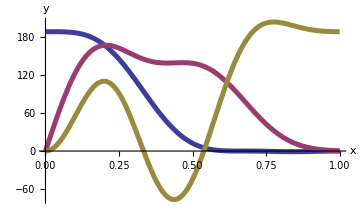
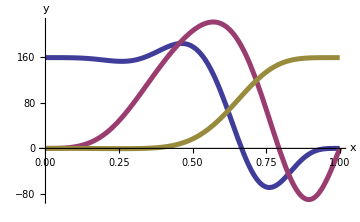

2

-0.09

0.0508925

0.145825

0.0371004

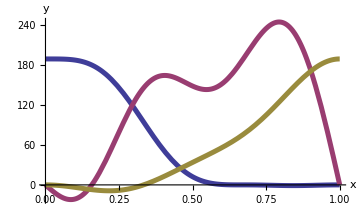
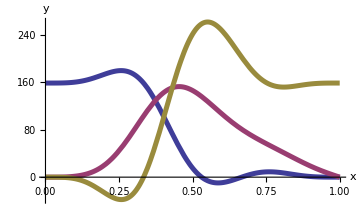

3

0.09+2.52425×10^-12 ⅈ

0.0508925

-0.0278406+0.0105344 ⅈ

-0.386696-0.205153 ⅈ

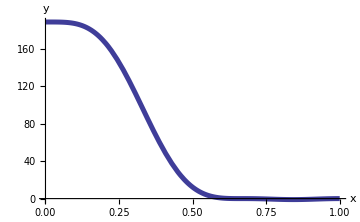
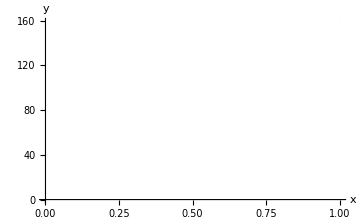

4

0.09-2.52425×10^-12 ⅈ

0.0508925

-0.0278406-0.0105344 ⅈ

-0.386696+0.205153 ⅈ

-Graphics--Graphics-

5

-0.09

0.0508925

0.0194301

0.0215904

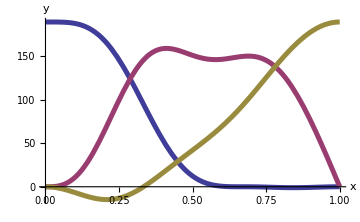
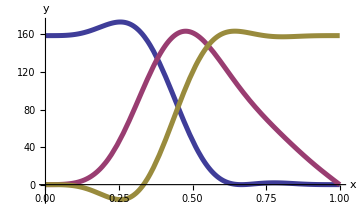

6

-0.09

0.0508925

0.0137953

0.0206895

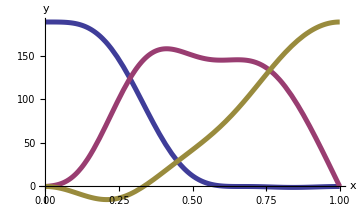
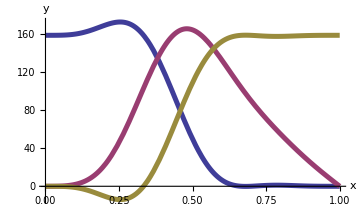

7

-0.09

0.0508925

0.00145148

0.065446

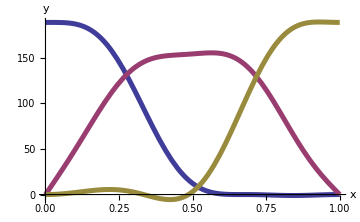
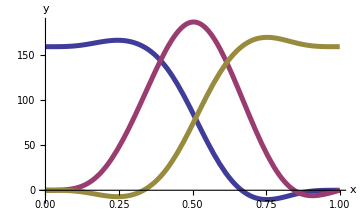

8

-0.09

0.0508925

0.0940404

0.152775

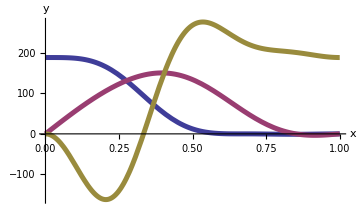
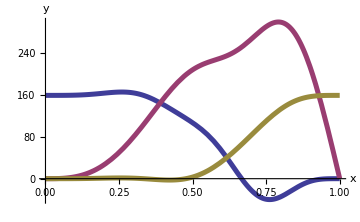

9

-0.09

0.0508925

1.66443

0.819224

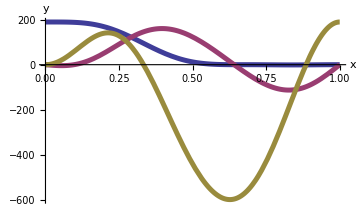
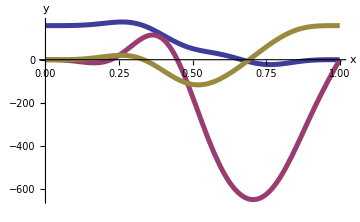

10

-0.09

0.0508925

19.7365

1.53029

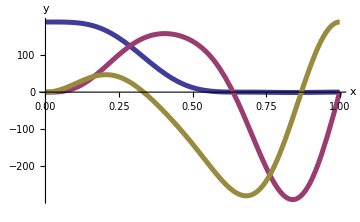
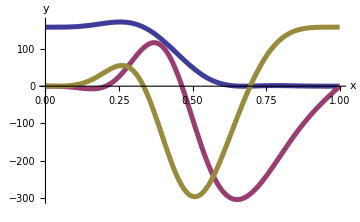

```mathematica
ph=100*(h[0]+2*Sum[h[i]*Cos[Pi*i*x],{i,1,K}]);
pb=100*2*Sum[b[i]*Sin[Pi*i*x],{i,1,L}];
pg=100*(g[0]+2*Sum[g[i]*Cos[Pi*i*x],{i,1,M}]);
pkh=100*(kh[0]+2*Sum[kh[i]*Cos[Pi*i*x],{i,1,K1}]);
pkb=100*2*Sum[kb[i]*Sin[Pi*i*x],{i,1,L1}];
pkg=100*(kg[0]+2*Sum[kg[i]*Cos[Pi*i*x],{i,1,M1}]);
pkhh=ph*pkh/300;
pkbb=pb*pkb/300;
pkgg=pg*pkg/300;

Do[Print[kk];
ssh=Sqrt[Sum[(h[Abs[i]]/.NSLv[[kk]])^2,{i,-K,K}]];
ssb=Sqrt[Sum[(b[Abs[i]]/.NSLv[[kk]])^2,{i,-L,L}]];
ssg=Sqrt[Sum[(g[Abs[i]]/.NSLv[[kk]])^2,{i,-M,M}]];
Print[((h[0]/.NSLv[[kk]])*(g[0]/.NSLv[[kk]])+2*(h[1]/.NSLv[[kk]])*(g[1]/.NSLv[[kk]]))/(ssh*ssg)];
Print[Sum[(h[i]/.NSLv[[kk]])^2,{i,2,K}]/((h[0]/.NSLv[[kk]])^2+2*(h[1]/.NSLv[[kk]])^2)];
Print[Sum[(b[i]/.NSLv[[kk]])^2,{i,2,L}]/((b[0]/.NSLv[[kk]])^2+2*(b[1]/.NSLv[[kk]])^2)];
Print[Sum[(g[i]/.NSLv[[kk]])^2,{i,2,M}]/((g[0]/.NSLv[[kk]])^2+2*(g[1]/.NSLv[[kk]])^2)];
Print[Plot[{ph/.NSLv[[kk]],pb/.NSLv[[kk]],pg/.NSLv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]},ImageSize->Medium],Plot[{pkh/.NSLv[[kk]],pkb/.NSLv[[kk]],pkg/.NSLv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]},ImageSize->Medium]],{kk,Length[NSLv]}]
(*kk=14;
Plot[{ph/.NSLv[[kk]],pb/.NSLv[[kk]],pg/.NSLv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]
Plot[{pkh/.NSLv[[kk]],pkb/.NSLv[[kk]],pkg/.NSLv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]
Plot[{pkhh/.NSLv[[kk]],pkbb/.NSLv[[kk]],pkgg/.NSLv[[kk]],(pkhh+pkbb+pkgg)/.NSLv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]*)
```

9

0.	0.00202806	0.	0.00279068	0.	-0.00204712

0.	0.	0.	0.	0.	0.

0.	0.	0.	0.	0.	0.

0.	-0.00396775	0.	-0.00231687	0.	0.00400505

-0.0221438	0.0211386	0.0297596	0.0290874	0.0186313	-0.0213373

-0.0487165	0.0119032	-0.0167578	0.0163793	-0.0711074	-0.0120151

0.	-0.132697	0.	-0.32117	0.	0.133945

0.208152	-0.0119032	-0.0167578	0.0163793	0.229058	0.0120151

0.500451	0.501538	-0.706083	0.708581	-0.492484	-0.506253

0.637743	0.791951	0.	0.	0.631804	0.783375

0.500451	0.501538	0.706083	-0.708581	-0.492484	-0.506253

0.208152	-0.0119032	0.0167578	-0.0163793	0.229058	0.0120151

0.	-0.132697	0.	0.32117	0.	0.133945

-0.0487165	0.0119032	0.0167578	-0.0163793	-0.0711074	-0.0120151

-0.0221438	0.0211386	-0.0297596	-0.0290874	0.0186313	-0.0213373

0.	-0.00396775	0.	0.00231687	0.	0.00400505

0.	0.	0.	0.	0.	0.

0.	0.	0.	0.	0.	0.

0.	0.00202806	0.	-0.00279068	0.	-0.00204712

-0.09

0.112584

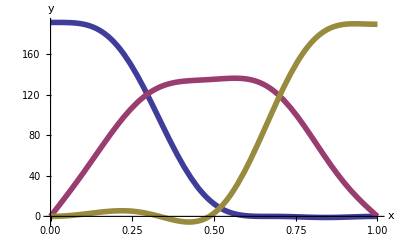

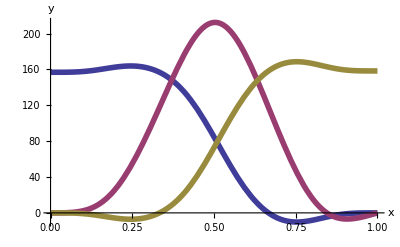

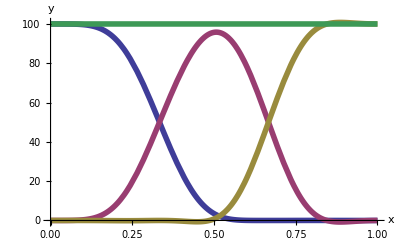

```mathematica
kk=7;(* 0.05 - 20 28 33 *) (* 0.01 - 25 *) (* 0 - 12 13 *) (* 0.03 - 24 27 28 *) (* 0.07 - 20 26 27 *) (* 0.1 - 20 29 30 31 34 *)
(*fs=OpenWrite["D:\Documents\Wavelets\W3 777 s014.txt",PageWidth->200]
SetOptions[fs, FormatType->StandardForm,CharacterEncoding-> "ASCII"]*)
KLM2=Max[K,K1,L,L1,M,M1]
min=10^-12;

Array[h2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,h2[i]=0.0];
For[i=-K,i≤K,i++,h2[i]=h[Abs[i]]/.NSLv[[kk]]];
Array[kh2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,kh2[i]=0.0];
For[i=-K1,i≤K1,i++,kh2[i]=kh[Abs[i]]/.NSLv[[kk]]];
shh=Sqrt[Sum[h2[i]^2,{i,-K,K}]];
skh=Sqrt[Sum[kh2[i]^2,{i,-K1,K1}]];

Array[g2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,g2[i]=0.0];
For[i=-M,i≤M,i++,g2[i]=g[Abs[i]]/.NSLv[[kk]]];
Array[kg2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,kg2[i]=0.0];
For[i=-M1,i≤M1,i++,kg2[i]=kg[Abs[i]]/.NSLv[[kk]]];
shg=Sqrt[Sum[g2[i]^2,{i,-M,M}]];
skg=Sqrt[Sum[kg2[i]^2,{i,-M1,M1}]];

Array[b2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,b2[i]=0.0];
For[i=-L,i≤L,i++,b2[i]=Sign[i]* b[Abs[i]]/.NSLv[[kk]]];
Array[kb2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,kb2[i]=0.0];
For[i=-L1,i≤L1,i++,kb2[i]=-Sign[i]*kb[Abs[i]]/.NSLv[[kk]]];
shb=Sqrt[Sum[b2[i]^2,{i,-L,L}]];
skb=Sqrt[Sum[kb2[i]^2,{i,-L1,L1}]];

(* нормировка по обратным функциям *)
(*For[i=-K,i≤K,i++,ss=h2[i]*skh;h2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-K1,i≤K1,i++,ss=kh2[i]/skh;kh2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-M,i≤M,i++,ss=g2[i]*skg;g2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-M1,i≤M1,i++,ss=kg2[i]/skg;kg2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-L,i≤L,i++,ss= b2[i]*skb;b2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-L1,i≤L1,i++,ss=kb2[i]/skb;kb2[i]=If[Abs[ss]<min,0.0,ss]];*)

(* нормировка по прямым функциям *)
For[i=-K,i≤K,i++,ss=h2[i]/shh;h2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-K1,i≤K1,i++,ss=kh2[i]*shh;kh2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-M,i≤M,i++,ss=g2[i]/shg;g2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-M1,i≤M1,i++,ss=kg2[i]*shg;kg2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-L,i≤L,i++,ss= b2[i]/shb;b2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-L1,i≤L1,i++,ss=kb2[i]*shb;kb2[i]=If[Abs[ss]<min,0.0,ss]];

(*For[i=-KLM2,i≤KLM2,i++,Print[kh2[i]]];*)
sep="\t";
(*For[i=-KLM2,i≤KLM2,i++,WriteString[fs,h2[i],sep,kh2[i],sep,b2[i],sep,kb2[i],sep,g2[i],sep,kg2[i],"\n"]];
Close[fs];*)
For[i=-KLM2,i≤KLM2,i++,Print[h2[i],sep,kh2[i],sep,b2[i],sep,kb2[i],sep,g2[i],sep,kg2[i]]];


ph2=100*(h2[0]+2*Sum[h2[i]*Cos[Pi*i*x],{i,1,KLM2}]);
pb2=100*2*Sum[b2[i]*Sin[Pi*i*x],{i,1,KLM2}];
pg2=100*(g2[0]+2*Sum[g2[i]*Cos[Pi*i*x],{i,1,KLM2}]);
pkh2=100*(kh2[0]+2*Sum[kh2[i]*Cos[Pi*i*x],{i,1,KLM2}]);
pkb2=-100*2*Sum[kb2[i]*Sin[Pi*i*x],{i,1,KLM2}];
pkg2=100*(kg2[0]+2*Sum[kg2[i]*Cos[Pi*i*x],{i,1,KLM2}]);
pkhh2=ph2*pkh2/300;
pkbb2=pb2*pkb2/300;
pkgg2=pg2*pkg2/300;

Print[h2[0]*g2[0]+2*h2[1]*g2[1]];
Print[kh2[0]*kg2[0]+2*kh2[1]*kg2[1]];
Plot[{ph2,pb2,pg2},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]
Plot[{pkh2,pkb2,pkg2},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]
Plot[{pkhh2,pkbb2,pkgg2,(pkhh2+pkbb2+pkgg2)},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]
```